```mathematica
ClearAll["Global`*"];
```

```mathematica
dataStandingVariation=Import[NotebookDirectory[]<>"../Data/"<>"Table_standing_variants_asexual.txt","CSV"];
```

```mathematica
dataAsexualSexual=Import[NotebookDirectory[]<>"../Data/"<>"Table_MGWP_Asexual_vs_Sexual_Avg.txt","CSV"];
dataAsexualSexualResistance=Import[NotebookDirectory[]<>"../Data/"<>"Table_MGWP_Asexual_vs_Sexual.txt","CSV"];
```

## Rescue probability and rescue year distribution depending on the investment in asexual vs. sexual reproduction

### Rescue probability

#### Parameters of the model

```mathematica
b= 0.9 140;
f=0.9 13000;
dZ=0.35;
gZ = 0.2;
dS=0.94;
c=0.3;
kc=0.5;
cr = {0,kc c,c};
```

```mathematica
g = 0.3;
p=0.95;
dB=0.48;
μ=10^-8;
hl=0.998;
ht=0.985;
kh=0.5;
densSeeds=80;
densPlants=1;
hL = {hl,(1-kh) hl, 0};
hT = {ht,(1-kh) ht, 0};
```

```mathematica
M={(1-μ)^2 {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+μ(1-μ) {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+μ^2{{0,0,0},{0,0.25,0.5},{0,0.5,1}},2 μ (1-μ) {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+((1-μ)^2 +μ^2) {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+2 μ (1-μ){{0,0,0},{0,0.25,0.5},{0,0.5,1}},μ^2 {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+μ {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+{{0,0,0},{0,0.25,0.5},{0,0.5,1}}}//N;
```

#### Standing genetic variation

```mathematica
v=dataStandingVariation⟦2;;,All⟧;
```

#### Rescue probability

```mathematica
pRescue[A_,q_, i_]:=1- Exp[A  (densPlants  (v[[i,2]]  (q[[1]]-1)+ v[[i,3]]  (q[[2]]-1)+v[[i,4]]  (q[[3]]-1))+densSeeds  (v[[i,2]]  (q[[4]]-1)+ v[[i,3]] (q[[5]]-1)+v[[i,4]]  (q[[6]]-1)))]//Quiet;
```

#### Variation of rhizome bud and seed numbers with investment in asexual vs. sexual reproduction

```mathematica
rate=((1-dZ)b gZ )/(f(1-dS)g/(1-(1-dB)(1-g)));
```

```mathematica
b=a 0.9 140;
f=(1+(1-a)rate)0.9 13000;
```

```mathematica
T=b(1-dZ)gZ;
S = (1-cr)f(1-dS);
```

```mathematica
asexual=((1-dZ)b gZ )/((1-dZ)b gZ +f(1-dS)g/(1-(1-dB)(1-g)));
```

#### Parameters of the offspring distributions

```mathematica
λ[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))g (1-hL[[j]])+KroneckerDelta[j,i]T(1-hT[[j]]);
λm[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))(1-g);
```

```mathematica
α=(1-dB) g (1-hL);
β=(1-dB) (1-g);
γ=(dB+(1-dB) g hL);
```

#### Parameters of the reduced set of equations for the extinction probabilities

```mathematica
Λ[i_,j_]:=λ[i,j]+λm[i,j]α[[j]]/(1-β);
Γ[i_]:=Exp[Sum[λm[i,j](γ[[j]]/(1-β)-1)-λ[i,j],{j,1,3}]];
```

#### Extinction probabilities

```mathematica
q={q1,q2,q3,(α[[1]]q1+γ[[1]])/(1-β),(α[[2]]q2+γ[[2]])/(1-β),(α[[3]]q3+γ[[3]])/(1-β)}/.Table[FindRoot[{q1==Γ[1]Exp[Λ[1,1] q1+Λ[1,2] q2+Λ[1,3] q3],q2==Γ[2]Exp[Λ[2,1] q1+Λ[2,2] q2+Λ[2,3] q3],q3==Γ[3]Exp[Λ[3,1] q1+Λ[3,2] q2+Λ[3,3] q3]},{{q1,0},{q2,0},{q3,0}}]//Quiet,{a,0,2,0.001}];
```

#### Rescue probability as a function of the proportion of asexually generated offspring

```mathematica
pR=MapThread[pRescue[10^4,#1,#2]&,{q,Range[1,Length[v[[All,1]]]]}];
```

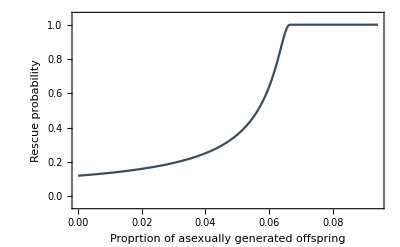

```mathematica
asexualSexualPlot =ListPlot[Partition[Riffle[Table[asexual,{a,0,2,0.001}],pR],2],PlotRange->{Automatic,{-.05,1.05}},Joined->True,Mesh->False,MeshStyle->PointSize[0.018],PlotStyle->Directive[Full,RGBColor["#3C4C59"]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Proprtion of asexually generated offspring","Rescue probability"}]
```

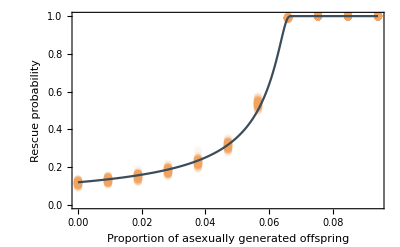

```mathematica
Show[ListPlot[Partition[Riffle[Flatten[ConstantArray[#,100]&/@Table[asexual,{a,0,2,0.2}]],dataAsexualSexual⟦2;;,3⟧],2],PlotStyle->Directive[RGBColor["#F2A35E"],PointSize[0.015],Opacity[0.1]]],asexualSexualPlot,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Proportion of asexually generated offspring","Rescue probability"}]
```

### Rescue probability if the herbicide efficacy on rhizome plants is not reduced

#### Parameters of the model that change

```mathematica
ht=0.998;
hT = {ht,(1-kh) ht, 0};
```

#### Parameters of the offspring distributions

```mathematica
λ[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))g (1-hL[[j]])+KroneckerDelta[j,i]T(1-hT[[j]]);
λm[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))(1-g);
```

#### Parameters of the reduced set of equations for the extinction probabilities

```mathematica
Λ[i_,j_]:=λ[i,j]+λm[i,j]α[[j]]/(1-β);
Γ[i_]:=Exp[Sum[λm[i,j](γ[[j]]/(1-β)-1)-λ[i,j],{j,1,3}]];
```

#### Extinction probabilities

```mathematica
q={q1,q2,q3,(α[[1]]q1+γ[[1]])/(1-β),(α[[2]]q2+γ[[2]])/(1-β),(α[[3]]q3+γ[[3]])/(1-β)}/.Table[FindRoot[{q1==Γ[1]Exp[Λ[1,1] q1+Λ[1,2] q2+Λ[1,3] q3],q2==Γ[2]Exp[Λ[2,1] q1+Λ[2,2] q2+Λ[2,3] q3],q3==Γ[3]Exp[Λ[3,1] q1+Λ[3,2] q2+Λ[3,3] q3]},{{q1,0},{q2,0},{q3,0}}]//Quiet,{a,0,2,0.001}];
```

#### Rescue probability as a function of the proportion of asexually generated offspring

```mathematica
pR=MapThread[pRescue[10^4,#1,#2]&,{q,Range[1,Length[v[[All,1]]]]}];
```

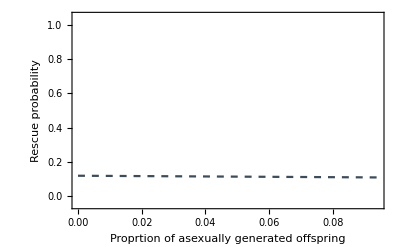

```mathematica
asexualSexualPlot2 =ListPlot[Partition[Riffle[Table[asexual,{a,0,2,0.001}],pR],2],PlotRange->{Automatic,{-.05,1.05}},Joined->True,Mesh->False,MeshStyle->PointSize[0.018],PlotStyle->Directive[Dashed,RGBColor["#3C4C59"]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Proprtion of asexually generated offspring","Rescue probability"}]
```

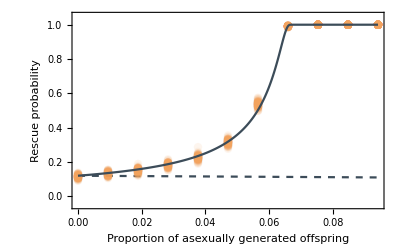

```mathematica
Show[asexualSexualPlot2,ListPlot[Partition[Riffle[Flatten[ConstantArray[#,100]&/@Table[asexual,{a,0,2,0.2}]],dataAsexualSexual⟦2;;,3⟧],2],PlotStyle->Directive[RGBColor["#F2A35E"],PointSize[0.015],Opacity[0.1]]],asexualSexualPlot,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Proportion of asexually generated offspring","Rescue probability"}]
```

### Rescue year distribution for different proportions of asexually generated offspring

```mathematica
dataAsexualSexualResistancePartitioned=Partition[dataAsexualSexualResistance⟦2;;⟧,10^5];
```

```mathematica
escaped=Table[DeleteCases[dataAsexualSexualResistancePartitioned⟦i,All,4⟧,"NaN"],{i,{5,6,7}}];
```

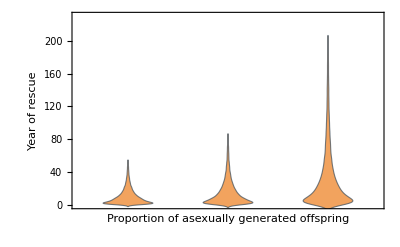

```mathematica
DistributionChart[escaped,ChartBaseStyle->EdgeForm[RGBColor["#3C4C59"]],ChartStyle->RGBColor["#F2A35E"],PlotRange->{{0.5,3.5},{0,230}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Proportion of asexually generated offspring","Year of rescue"}]
```